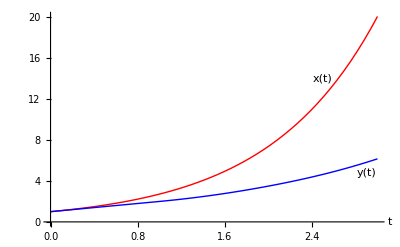

```mathematica
ClearAll;
f[x_[t_]]:=x'[t]-x[t];
g[x_[t_]]:=x'[t]-x[t-1];
sol1:=NDSolve[{f[x[t]]==0,x[0]==1},x,{t,0,3}];
sol2:=NDSolve[{g[x[t]]==0,x[t/;t<0]==1},x,{t,0,3}];
p1:=Plot[Evaluate[x[t]/.sol1],{t,0,3},PlotStyle->Red];
p2:=Plot[Evaluate[x[t]/.sol2],{t,0,3},PlotStyle->Blue];
Show[p1,p2,AxesLabel->{"t",""},Epilog->{Style[Text["x(t)",{2.5,14}],12],Style[Text["y(t)",{2.9,4.8}],12]}]
```